```mathematica
Clear[z]
```

```mathematica
R=10;
v0=0 1/R^(3/2)R;
```

```mathematica
DD[r_,ϕ_,z_]:=√(R^2+r^2-2R r Cos[ϕ]+z^2)
zfac[r_,ϕ_,z_]:=(-r v0 Sin[ϕ])/DD[r,ϕ,z]
```

```mathematica
EE[r_]:=R NIntegrate[1/(1+zfac[r,ϕ,z])^4 √(1-(z/DD[r,ϕ,z])^2)1/DD[r,ϕ,z]^2,{z,-Infinity,+Infinity},{ϕ,0,2π},Method->"MonteCarlo",MaxPoints->100000]
Fr[r_]:=R NIntegrate[1/(1+zfac[r,ϕ,z])^4 √(1-(z/DD[r,ϕ,z])^2)1/DD[r,ϕ,z]^2(R Cos[ϕ]-r)/DD[r,ϕ,z],{z,-Infinity,+Infinity},{ϕ,0,2π},Method->"MonteCarlo",MaxPoints->10000]
```

```mathematica
EE[r_,ϕ_]:=R NIntegrate[√(1-(z/DD[r,ϕ,z])^2)1/DD[r,ϕ,z]^2,{z,-Infinity,+Infinity}]
Fr[r_,ϕ_]:=R NIntegrate[√(1-(z/DD[r,ϕ,z])^2)1/DD[r,ϕ,z]^2(R Cos[ϕ]-r)/DD[r,ϕ,z],{z,-Infinity,+Infinity}]
```

```mathematica
EE[.99999999R,0]
```

1.18633×10^8

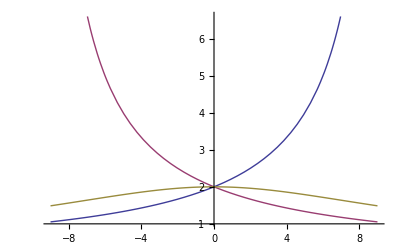

```mathematica
Plot[{EE[r,0],EE[r,π],EE[r,π/2]},{r,-9,9.}]
```

```mathematica
Fr[4]
```

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.000954417 and 0.00271551 for the integral and error estimates.

0.00954417

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 0.000743504 and 0.0263876 for the integral and error estimates.

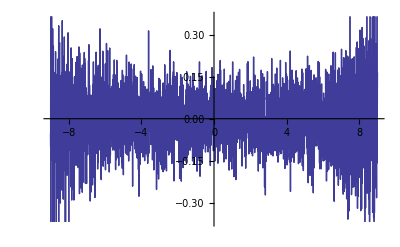

```mathematica
Plot[{Fr[r]},{r,-9,9.}]
```

```mathematica
DDrod[R_,z_]:=√(R^2+z^2)
EErod[R_]:=NIntegrate[√(1-(z/DDrod[R,z])^2)1/DDrod[R,z]^2,{z,-Infinity,+Infinity}]
```

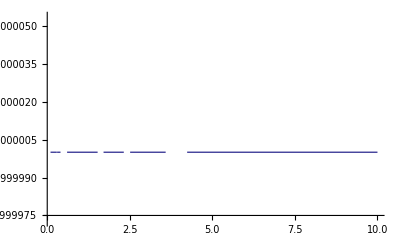

```mathematica
Plot[{EErod[R]R},{R,.1,10}]
```